# Partial Differential Equations

## Analytics

Consider the Liouville Equation

```mathematica
Leq=D[ϕ[x,y], {x,2}]+D[ϕ[x,y], {y,2}]+Exp[-2 ϕ[x,y]];
```

Pedro guarantees the solution is of this form

```mathematica
Subscript[ϕ, 0][x_,y_]=c Log[(1-f[x-ⅈ y] g[x+ⅈ y])^2/(d f'[x-ⅈ y] g'[x+ⅈ y])];
```

We can fix the constants by inspection

```mathematica
Leq/.ϕ-> Subscript[ϕ, 0]/.c-> 1/2/.d->4//FullSimplify
```

0

We can now define the correct solution

```mathematica
Subscript[ϕ, 0][x_,y_]=1/2 Log[(1-f[x-ⅈ y] g[x+ⅈ y])^2/(4 f'[x-ⅈ y] g'[x+ⅈ y])];
```

We may now want to plot this. We may suggest f(x)=x or g(x)=x^2

```mathematica
Subscript[ϕ, 1][x_,y_]=(Subscript[ϕ, 0][x,y]/.{f->(1+Exp[2 #]&),g->(1+Exp[2#]&)})//FullSimplify;
```

```mathematica
analytic=Plot3D[Subscript[ϕ, 1][x,y],{x,0,1},{y,0,1},PlotRange->All,PlotStyle->Red]
```

-Graphics3D-

## Numerics

We now want to fix the solution at the boundary of the square [0,1]×[0,1] and find the solution of

```mathematica
Leq=D[ϕ[x,y], {x,2}]+D[ϕ[x,y], {y,2}]+Exp[-2 ϕ[x,y]]
```

ⅇ^(-2 ϕ[x,y])+ϕ^(0,2)[x,y]+ϕ^(2,0)[x,y]

We will use the relaxation method. This equation, in a discretized form is (∂^2 ϕ(x,y))/(∂x^2)+(∂^2 ϕ(x,y))/(∂y^2)→Λ((∂ϕ(x_(i+1),y_j))/(∂x_(i+1))-(∂ϕ(x_i,y_j))/(∂x_i)+(∂ϕ(x_i,y_(j+1)))/(∂y_(j+1))-(∂ϕ(x_i,y_j))/(∂y_j))→ Λ^2(ϕ(x_(i+1),y_j)-ϕ(x_i,y_j)-ϕ(x_i,y_j)-ϕ(x_(i-1),y_j)+ϕ(x_i,y_(j+1))-ϕ(x_i,y_j)-ϕ(x_i,y_j)-ϕ(x_i,y_(j-1)))= (2Λ)^2/4(ϕ(x_(i+1),y_i)+ϕ(x_(i-1),y_i)+ϕ(x_i,y_(i+1))+ϕ(x_i,y_(i-1))-4ϕ(x_i,y_i)), where we have discretized the region as {x_0,...,x_Λ}×{y_0,...,y_Λ} with x_i=y_i=i/Λ and Λ∈. This has the very nice interpretation of being, up to a constant, the difference between the value of a function at a point and the average it takes around that point. Therefore, solutions of Laplace’s equation Δϕ=0 are precisely those functions whose values are equal to the local average value of the function.

```mathematica
G[n_]:=G[n]=G[n-1]+n G[n-2]
G[0]=1;
G[1]=2;
```

```mathematica
G[100]
```

253432098810473036968111090447973896728572522374012678663012251250290473349127602176

```mathematica
Λ=20;
```

```mathematica
ClearAll[ψ]

ψ[n_][0,y_]=Subscript[ϕ, 1][0,y];
ψ[n_][1,y_]=Subscript[ϕ, 1][1,y];
ψ[n_][x_,0]=Subscript[ϕ, 1][x,0];
ψ[n_][x_,1]=Subscript[ϕ, 1][x,1];

ψ[1][x_,y_]=2;

ψ[n_][x_,y_]:=ψ[n][x,y]=1/4(ψ[n-1][x+1/Λ,y]+ψ[n-1][x-1/Λ,y]+ψ[n-1][x,y+1/Λ]+ψ[n-1][x,y-1/Λ]+1./(4 Λ^2)Exp[-2ψ[n-1][x,y]]);
```

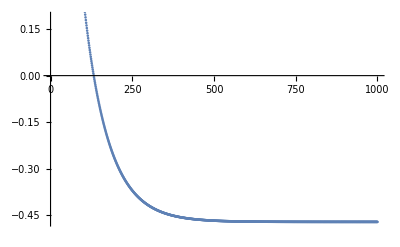

```mathematica
Table[{n,ψ[n][5/Λ,10/Λ]},{n,1,1000}]//ListPlot
```

```mathematica
ClearAll[num]
num[m_]:=num[m]=ListPlot3D[Flatten[Table[{j/Λ,k/Λ,ψ[m][j/Λ,k/Λ]//Re},{j,0,Λ},{k,0,Λ}],1],PlotRange->All,PlotStyle->Opacity[.5]]
```

```mathematica
Show[num[#],analytic] & /@{5,20,100,500,1000}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}